```mathematica
(*derivative for input-output function evaluated at Isyn=2 Ith/c*)
c=615;g=.087; Ith=177;  (*excitatory: c=310;g=.16; Ith=125;*) (*c=615;g=.087; Ith=177;*)
```

```mathematica
c(1-Exp[-g(Ith)])^(-1)-(Ith)(1-Exp[-g(Ith)])^(-2) (c g Exp[-g(Ith)])
```

614.998

```mathematica
Clear[c,g,Ith];
```

```mathematica
(*linear estimate for excitaory and inhibitory input-output functions*) k1 = 310/1000;k2=615/1000 ;(*1/1000 factor as in KF's paper*);
```

```mathematica
Jee=0.541794;Jie=1/10;Jei=.05;Jii=1/10;a=64/100;
```

```mathematica
ti=2 ; te= 100;   c = 250 (*gain factor*); Io= 1/10 (*background*); Ith= 150;Is=1/20(*stimulus*);
```

```mathematica
c1=a (c(Is+Io)-Ith)
```

-(225 a)/2

```mathematica
c2=a c Jee;
```

```mathematica
c3=a c Jie;
```

```mathematica
c4= c Io-Ith;
```

```mathematica
c5=c Jei;
```

```mathematica
c6=c Jii;
```

```mathematica
c10=k1 c2 -1/te -k1 c1 +(c4-c2)k1 c3 k2 /(1/ti +k2 c6)
```

-1/100+(279 a)/8+(155 a Jee)/2+(3813 a (-125-250 a Jee) Jie)/(80 (1/2+(615 Jii)/4))

```mathematica
c9=k1 c3 k2 c2/(1/ti+k2 c6-k1 c2)
```

(95325 a^2 Jee Jie)/(8 (1/2-(155 a Jee)/2+(615 Jii)/4))

```mathematica
c11=k1 c1-k1 c3 k2 c4/(1/ti +k2 c6)
```

-(279 a)/8+(95325 a Jie)/(16 (1/2+(615 Jii)/4))

```mathematica
k1 c1
```

-(279 a)/8

```mathematica
Se=(-c10-Sqrt[c10 ^2-4 c9 c11])/(2 c9);
```

```mathematica
Si=k2(c4+c2 Se)/(1/ti + k2 c6);
```

```mathematica
c7 = 1/te-k1 c2 +2 k1 c2 Se+1/ti +k2 c6;
```

```mathematica
c8=1/(te ti)+k2 c6/(te)-k1 c2/ti -k1 c1 k2 c6 + 2 k1 c2 Se/ti+k1 k2 c5 c3+2 k2 c6 k1 c2 Se -k1 k2 c3 c5 Se;
```

```mathematica
Jee=0.541794691013832;
```

```mathematica
Si
```

1/(200 (1/2+(615 Jii)/4))123 (-125+1/(3813 a Jie)40 (1/2-41.9891 a+(615 Jii)/4) (1/100-76.8641 a-(3813 (-125-135.449 a) a Jie)/(80 (1/2+(615 Jii)/4))-√(-(25823.3 a^2 Jie (-(279 a)/8+(95325 a Jie)/(16 (1/2+(615 Jii)/4))))/(1/2-41.9891 a+(615 Jii)/4)+(-1/100+76.8641 a+(3813 (-125-135.449 a) a Jie)/(80 (1/2+(615 Jii)/4)))^2)))

```mathematica
Clear[Jie,Jee,Jie,Jei]
```

```mathematica
Clear[Jie]
```

```mathematica
Jii=1/100;Jie=1/100;
```

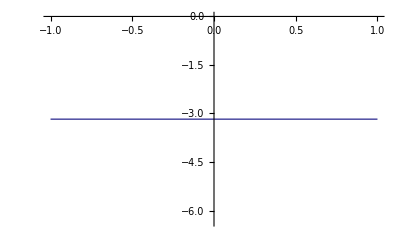

```mathematica
Plot[Si,{Jee,-1,1}]
```

```mathematica
(*Hopf bifurcation with different c (gain) and Ith for excitatory and inhibitory units*)
(*derivative for input-output function evaluated at Isyn=2 Ith/c*)
c=615;g=.087; Ith=177;  (*excitatory: c=310;g=.16; Ith=125;*) (*inhibitory: c=615;g=.087; Ith=177;*)
```

```mathematica
c(1-Exp[-g(Ith)])^(-1)-( Ith)(1-Exp[-g(Ith)])^(-2) (c g Exp[-g( Ith)])
```

614.998

```mathematica
(*test plot for input output function*)
```

```mathematica
k2
```

123/200

```mathematica
<<PlotLegends`
```

```mathematica
tr=2;
```

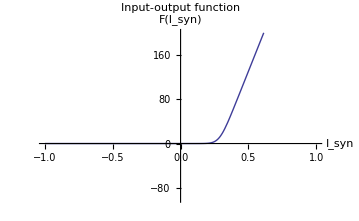

```mathematica
Plot[(ci I-iIth)/(1-Exp[-g (ci I - iIth)])+tr/1000(ci I-iIth) ,{I,-1,1},AxesLabel->{"I_syn","F(I_syn)"},PlotRange->{-100,200},PlotLabel->"Input-output function"]
```

```mathematica
iIth/ci
```

59/205

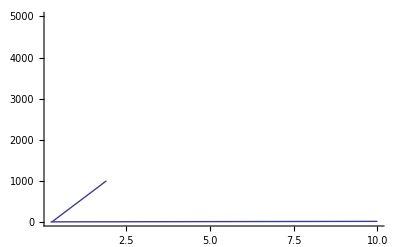

```mathematica
Show[p1,p2,PlotRange->{0,5000}]
```

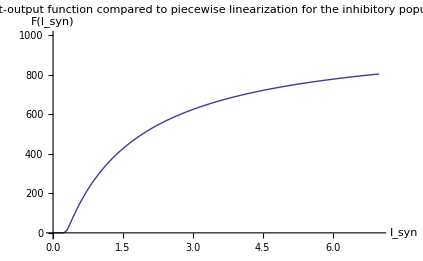

```mathematica
refi1=Plot[(ci x-iIth)/(1-Exp[-gi (ci x - iIth)]+tri/1000(ci x-iIth) ),{x,0,7},PlotRange->{-10,1000},AxesLabel->{"I_syn","F(I_syn)"},PlotLabel->"Input-output function compared to piecewise linearization 
for the inhibitory population"]
```

```mathematica
Needs["PlotLegends`"];
```

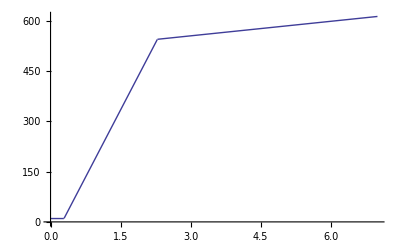

```mathematica
refi2=Plot[Piecewise[{{10,x<iIth/ci},{534.5275/2(x-iIth/ci)+10,iIth/ci<x<iIth/ci+2},{14.45(x-iIth/ci-2)+544.5,x>iIth/ci+2}}],{x,0,7} ]
```

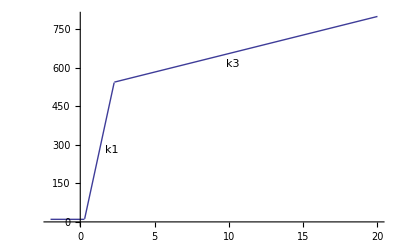

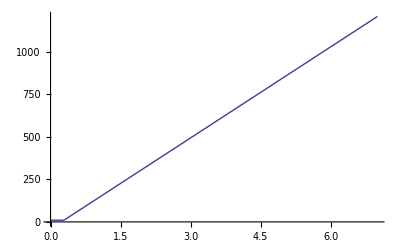

```mathematica
refi2=Plot[Piecewise[{{10,x<iIth/ci},{534.5275/3(x-iIth/ci)+10,iIth/ci<x<iIth/ci+20}}],{x,0,7} ]
```

```mathematica
N[(800-544)/(18-iIth/ci)]
```

14.4533

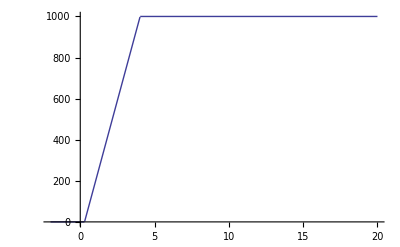

```mathematica
534.5275
```

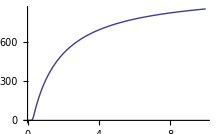

```mathematica
Plot[(ci x-iIth)/(1-Exp[-g(ci x-iIth)]+tri/1000(ci x-iIth)),{x,0,10}]
```

```mathematica
N[iIth/ci]
```

0.287805

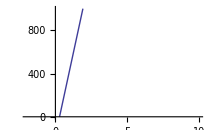

```mathematica
p2=Plot[ci x -iIth,{x,-2,10},PlotRange->{0,1000}]
```

```mathematica
D[(c I1-Ith)/(1-Exp[-g (c I1 - Ith)]),I1]/.I1->10
```

c/(1-ⅇ^(-0.087 (10 c-Ith)))-(0.087 c ⅇ^(-0.087 (10 c-Ith)) (10 c-Ith))/((1-ⅇ^(-0.087 (10 c-Ith)))^2)

```mathematica
Clear[g]
```

```mathematica
D[D[(c I1-Ith)/(1-Exp[-g (c I1 - Ith)]),I1],I1]
```

-(2 c^2 ⅇ^(-g (c I1-Ith)) g)/((1-ⅇ^(-g (c I1-Ith)))^2)+(2 c^2 ⅇ^(-2 g (c I1-Ith)) g^2 (c I1-Ith))/((1-ⅇ^(-g (c I1-Ith)))^3)+(c^2 ⅇ^(-g (c I1-Ith)) g^2 (c I1-Ith))/((1-ⅇ^(-g (c I1-Ith)))^2)

```mathematica
D[(ci I1-iIth)/(1-Exp[-g (ci I1 - iIth)]+tr/1000(ci I1-iIth) ),I1]
```

-((123/200+53.505 ⅇ^(-0.087 (-177+615 I1))) (-177+615 I1))/((1-ⅇ^(-0.087 (-177+615 I1))+(-177+615 I1)/1000)^2)+615/(1-ⅇ^(-0.087 (-177+615 I1))+(-177+615 I1)/1000)

```mathematica
D[(ce I1-eIth)/(1-Exp[-g (ce I1 - eIth)]+tre/1000(ce I1-eIth) ),I1]
```

-((31/50+26.97 ⅇ^(-0.087 (-125+310 I1))) (-125+310 I1))/((1-ⅇ^(-0.087 (-125+310 I1))+1/500 (-125+310 I1))^2)+310/(1-ⅇ^(-0.087 (-125+310 I1))+1/500 (-125+310 I1))

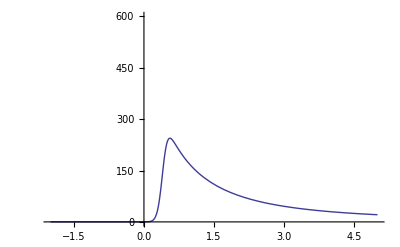

```mathematica
Plot[-((31/50+26.97 ⅇ^(-0.087 (-125+310 I1))) (-125+310 I1))/((1-ⅇ^(-0.087 (-125+310 I1))+1/500 (-125+310 I1))^2)+310/(1-ⅇ^(-0.087 (-125+310 I1))+1/500 (-125+310 I1)),{I1,-2,5},PlotRange->{0,600}]
```

```mathematica
FindMaximum[-((31/50+26.97 ⅇ^(-0.087 (-125+310 I1))) (-125+310 I1))/((1-ⅇ^(-0.087 (-125+310 I1))+1/500 (-125+310 I1))^2)+310/(1-ⅇ^(-0.087 (-125+310 I1))+1/500 (-125+310 I1)),I1]
```

{244.363,{I1→0.556311}}

```mathematica
(*for inhibitory pop, max slope=534.5275299643712, divide by 2 to average. at{I->0.38173489267836197}. For excitatory pop, max slope=244.3629893416042, at{I->0.5563112032321061*)
```

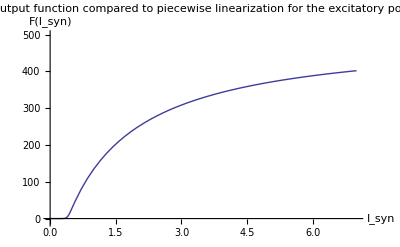

```mathematica
refe1=Plot[(ce x-eIth)/(1-Exp[-ge (ce x - eIth)]+tre/1000(ce x-eIth) ),{x,0,7},PlotRange->{-10,500},AxesLabel->{"I_syn","F(I_syn)"},PlotLabel->"Input-output function compared to piecewise linearization 
for the excitatory population"]
```

```mathematica
refe2=Plot[Piecewise[{{10,x<eIth/ce},{244.362989341/2(x-eIth/ce)+10,eIth/ce<x<eIth/ce+2.8},{5.75(x-eIth/ce-2.8)+1.4*244+10,x>eIth/ce+2.8}}],{x,0,7} ]
```

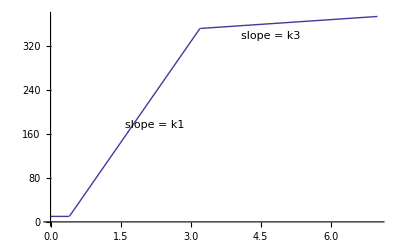

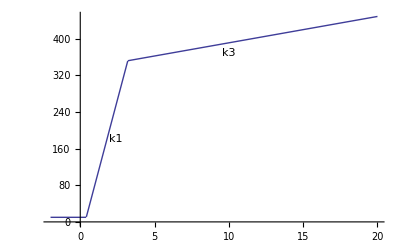

```mathematica
refe2=-Graphics-
```

-Graphics-

```mathematica
(450-10-1.4*244)/(17.5-eIth/ce)
```

5.75547

```mathematica
c=615;Ith=177;g=.087;
```

```mathematica
Jee=0.541794;Jie=1/10;Jei=.05;Jii=1/10;
```

```mathematica
(*ce for excitatory gain, ci for inhibitory gain. eIth and iIth the different thresholds *)
ti=2 ; te= 100;   ce = 310 (*gain factor*); ci= 615; Io= 1/10 (*background*); eIth= 125;iIth= 177; Is=1/20(*stimulus*);a=64/100; (*linear estimate for excitaory and inhibitory input-output functions*) k1 = 310/1000;k2=615/1000 ;(*1/1000 for unit consistency*);
```

```mathematica
c1=a (ce(Is+Io)-eIth)
```

-1256/25

```mathematica
c2=a ce Jee
```

107.492

```mathematica
c3=a ce Jie
```

496/25

```mathematica
c4= ci Io-iIth
```

-231/2

```mathematica
c5=ci Jei
```

30.75

```mathematica
c6=ci Jii
```

123/2

```mathematica
c10=k1 c2 -1/te -k1 c1 +(c4-c2)k1 c3 k2 /(1/ti +k2 c6)
```

26.8772

```mathematica
c9=k1 c3 k2 c2/(1/ti+k2 c6-k1 c2)
```

81.3175

```mathematica
c11=k1 c1-k1 c3 k2 c4/(1/ti +k2 c6)
```

-39992914/9580625

```mathematica
k1 c1
```

-9734/625

```mathematica
Se=(-c10-Sqrt[c10 ^2-4 c9 c11])/(2 c9)
```

-0.445698

```mathematica
Si=k2(c4+c2 Se)/(1/ti + k2 c6)
```

-2.62239

```mathematica
c7 = 1/te-k1 c2 +2 k1 c2 Se+1/ti +k2 c6
```

-24.6936

```mathematica
c8=1/(te ti)+k2 c6/(te)-k1 c2/ti -k1 c1 k2 c6 + 2 k1 c2 Se/ti+k1 k2 c5 c3+2 k2 c6 k1 c2 Se -k1 k2 c3 c5 Se
```

-397.378

```mathematica
Jee=0.541794691013832;
```

```mathematica
Clear[Jie,Jee,Jie,Jei]
```

```mathematica
Clear[Jie]
```

```mathematica
Jii=1/100;Jie=1/100;
```